```mathematica
Часть 1. Прямой подсчёт суммы
```

```mathematica
Необходимые функции
```

```mathematica
f[k_,σ_]:=If[
SelectFirst[Drop[σ,k],#>Max[Take[σ,k]]&, "NotFound"]≠"NotFound",
     If[
SelectFirst[Drop[σ,k],#>Max[Take[σ,k]]&,"NotFound"]==Max[σ],
 1,0], 
0];
Sn[n_]:=Permutations[Range[n]];
p[n_,k_]:=1/(n!)∑_(i=1)^(n!) f[k,Sn[n][[i]]];
p[n_,k_, Sn_]:=1/(n!)∑_(i=1)^(n!) f[k,Sn[[i]]]; (*Для подсчёта при n=8,9,10*)
pHard[n_,k_]:=Mean[(f[k,#]&)/@Sn[n]];
pHard[n_,k_, Sn_]:=Mean[(f[k,#]&)/@Sn];
FindTopK[Lst_]:=FirstPosition[Lst,Max[Lst]][[1]];
```

```mathematica
Прямой подсчёт с замером времени
```

```mathematica
Sn8 = Sn[8];
lst8 =Table[pHard[8,k, Sn8],{k,1,8}];
Sn9 = Sn[9];  
lst9 =Table[pHard[9,k, Sn9],{k,1,9}];
Time1=AbsoluteTiming[
Sn10=Sn[10];
lst10=Table[pHard[10,k, Sn10],{k,1,10}];
][[1]]
```

367.558

```mathematica
FindTopK[lst8]
```

3

```mathematica
FindTopK[lst9]
```

3

```mathematica
FindTopK[lst10]
```

3

```mathematica
Визуализация графиков
```

```mathematica
График Subscript[P, n,k] для значений n=2,...,7
```

```mathematica
Manipulate[ListPlot[Table[pHard[n,k], {k,1,n}]],{n, 2, 7,1}]
```

```mathematica
График Subscript[P, n,k] для значений n=8
```

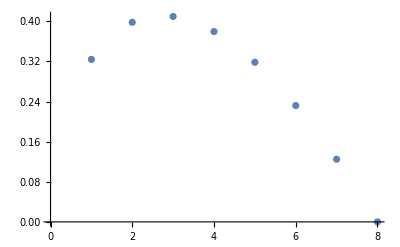

```mathematica
ListPlot[lst8]
```

```mathematica
График Subscript[P, n,k] для значений n=9
```

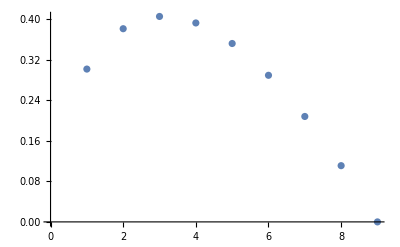

```mathematica
ListPlot[lst9]
```

```mathematica
График Subscript[P, n,k] для значений n=10
```

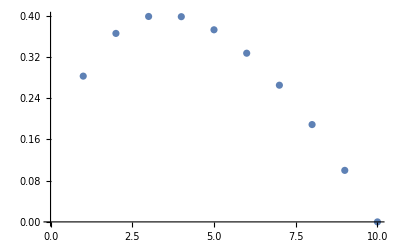

```mathematica
ListPlot[lst10]
```

```mathematica
Часть 2.  Приближённый подсчёт.
```

```mathematica
Необходимые функции
```

```mathematica
RandPerm[n_, NN_]:= Table[RandomSample[Range[n]], {i,1,NN}];

pPribl[k_, σs_]:=1/(Dimensions[σs][[1]])∑_(i=1)^(Dimensions[σs][[1]]) f[k,σs[[i]]];
pPriblHard[k_, σs_]:=Mean[(f[k, #]&)/@σs];
```

```mathematica
Подсчёт с замером времени
```

```mathematica
SeedRandom[2019];
Time2= AbsoluteTiming[
σs=RandPerm[1000, 200];
pribls=Table[pPriblHard[k, σs], {k,1,1000}];
][[1]]
```

260.927

```mathematica
FindTopK[pribls]
```

289

```mathematica
Визуализация результатов
```

```mathematica
График приближенных значений Subscript[P, n,k]
```

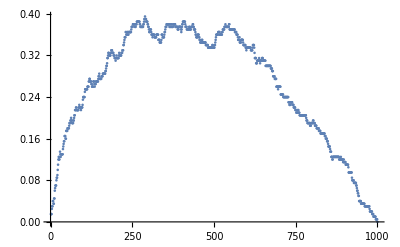

```mathematica
ListPlot[pribls]
```

```mathematica
Часть 3. Интерполяция
```

```mathematica
Интерполяция Хермита
```

```mathematica
Необходимые функции
```

```mathematica
interList[n_, step_]:=Sort[Prepend[Table[k,{k, step, n, step}],1]];
interFunc[lst_]:=ListInterpolation[ lst, {1, 1000}];
FindTopInterK[f_]:=Round[NMaximize[{f[x],20<x<500},x][[2,1,2]]];
```

```mathematica
Посчёт с замером времени
```

```mathematica
SeedRandom[2019];
Time31=AbsoluteTiming[
ks=interList[1000, 100];
σs=RandPerm[1000, 200];
pribls2=((pPribl[#, σs]&)/@ks); 
g=interFunc[pribls2];
][[1]]
```

2.56053

```mathematica
FindTopInterK[g]
```

327

```mathematica
Визуализация результатов
```

```mathematica
Приближенные значения Subscript[P, n,k] и график интерполяции Хермита
```

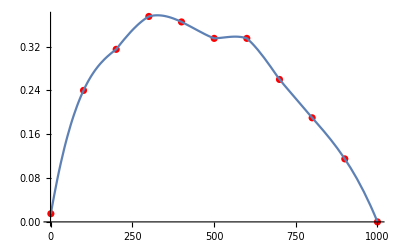

```mathematica
LPlt1= ListPlot[pribls2, DataRange->{1, 1000}, PlotStyle->{Thick,Red}];
plt1= Plot[g[x],{x,1,1000}];
Show[LPlt1, plt1 ]
```

```mathematica
Метод наименьших квадратов (для кубической параболы)
```

```mathematica
Необходимые  функции
```

```mathematica
fitFunc[data_]:=Fit[data, {1,x,x^2,x^3},x];
FindTopFitK[f_]:=Round[Maximize[{f,20<x<500},x][[2,1,2]]];
```

```mathematica
Подсчёт с замером времени
```

```mathematica
SeedRandom[2019];
Time32= AbsoluteTiming[
ks=interList[1000, 100];
σs=RandPerm[1000, 200];

pribls3=((pPriblHard[#, σs]&)/@ks); 

lstFit=Transpose[{ks, pribls3}];
h =fitFunc[lstFit];
][[1]]
```

2.57366

```mathematica
FindTopFitK[h]
```

396

```mathematica
Визуализация результатов
```

```mathematica
Приближенные значение Subscript[P, n,k] и график интерполяции МНК
```

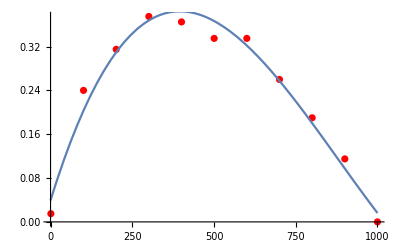

```mathematica
h =fitFunc[lstFit];
plt2= Plot[h,{x,0,1000}];
Show[LPlt1, plt2]
```

```mathematica
4. Нахождение Kmin и Kmax.
```

```mathematica
Необходимые функции
```

```mathematica
Kmax[σ_]:=Position[σ, SelectFirst[σ, #==Max[σ]&]][[1,1]];Kmin[σ_]:=If[Kmax[σ]>1,Position[Take[σ,Kmax[σ]-1],Max[Take[σ,Kmax[σ]-1]]][[1,1]],1];
getInd[point_]:=⌈point/100⌉;
IntegralP[n_,k_]:=Integrate[z, {x,y}∈ImplicitRegion[{0≤ kmin≤k≤kmax≤n},{kmin, kmax}]]/Integrate[z, {x,y}∈ ImplicitRegion[{0≤ kmin≤kmax≤n},{kmin, kmax}]];

countValues[lsts_]:=Table[ Length[Select[lsts, 100*(i-1)<#[[2]]≤ 100*(i)&]   ∩     Select[lsts,  100*(j-1)<#[[1]]≤ 100j&]] , {i,10}, {j, 10}] ;
```

```mathematica
Вычисления с подсчётом времени
```

```mathematica
SeedRandom[2019]
Time4=AbsoluteTiming[
ks=interList[1000, 100];
σs=RandPerm[1000, 200];
points= {Kmin[#],Kmax[#]}&/@σs;

MatVals = countValues[points] ;
values=(MatVals[[ getInd[#][[2]], getInd[#][[1]]]]&)/@points;
pointsAndValues=Append[Transpose[points], values ] // Transpose;
Polynoms=Table[Table[x^i*y^(j-i),{i,0,j}],{j,0,5}] // Flatten;
z=Fit[pointsAndValues, Polynoms , {x,y}];
valuesList = IntegralP[1000, #]&/@ks;
lstFit=Transpose[{ks, valuesList}];
pltFunc =fitFunc[lstFit];

][[1]]
```

2.67406

```mathematica
FindTopFitK[pltFunc]
```

398

```mathematica
Визуализация результатов
```

```mathematica
Разброс точек в осях Kmin,Kmax
```

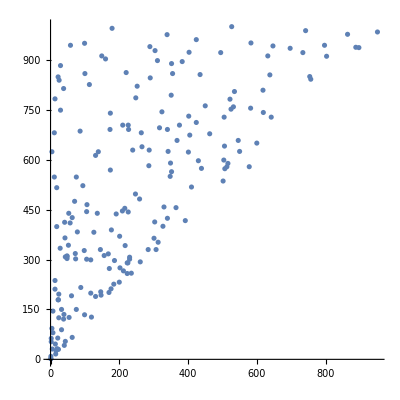

```mathematica
ListPlot[points, AspectRatio->1]
```

```mathematica
Гистограмма разброса точек
```

```mathematica
Histogram3D[points, {10,10} ,"Count"]
```

-Graphics3D-

```mathematica
Приближенная плотность вероятности, полученная МНК
```

```mathematica
Plot3D[z, {x, 0, 1000}, {y,0, 1000},RegionFunction->Function[{x,y, z},y≥x]]
```

-Graphics3D-

```mathematica
Итоговый график Subscript[P, n,k]
```

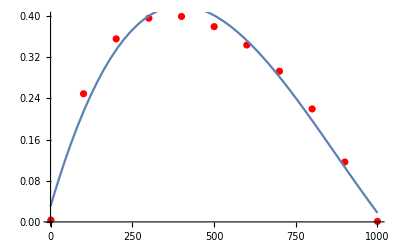

```mathematica
plt= Plot[pltFunc,{x,0,1000}];
LPlt= ListPlot[valuesList, DataRange->{1, 1000}, PlotStyle->{Thick,Red}];
Show[LPlt, plt]
```

```mathematica
Время затраченное на разных этапах работы
```

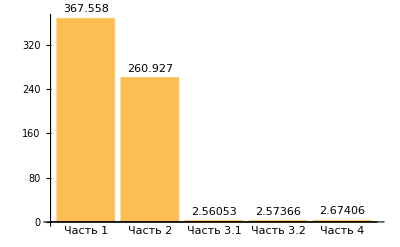

```mathematica
BarChart[{Time1,Time2,Time31,Time32,Time4}, ChartLabels->Placed[{{"Часть 1","Часть 2","Часть 3.1","Часть 3.2","Часть 4"},{Time1,Time2,Time31,Time32,Time4}},{Below, Above}]]
```